# MDL en Redes Bayesianas

### Autor: Carlos Manuel Rodríguez Martínez E-Mail: fis.carlosmanuel@gmail.com

## Resumen

Se implementa un algoritmo capaz de buscar el mejor modelo bajo la métrica MDL (Minimum Description Length), la cual mide qué tan bien se comprime un conjunto de datos bajo un modelo. El algoritmo procede a generar todos los DAG y evaluar la puntuación MDL dado un conjunto de datos. Se selecciona el grafo con menos puntuación MDL como el mejor modelo para describir los datos.

Referencia:
Levine, Nicholas D., “Using Minimum Description Length for Discretization Classification of Data Modeled by Bayesian Networks” (2011). Applied Mathematics Graduate Theses & Dissertations. 21. 
https://scholar.colorado.edu/appm_gradetds/21

## Implementación

## Generador DAGs

El algoritmo se divide en tres secciones. La primera sección corresponde al generador de DAGs, el cual selecciona los grafos que corresponden a un DAG por medio de los eigenvalores de su matriz de adyacencia.

```mathematica
BuildMatrix[paramList_,n_]:=Block[{parts},
parts = Partition[paramList,n-1];
Table[Insert[parts[[i]],1,i],{i,1,n}]
];
```

```mathematica
GeneratePossible[n_]:=Map[BuildMatrix[#,n]&,Tuples[{0,1},n(n-1)]];
```

```mathematica
CheckComplex[l_]:=Apply[Or,Map[MatchQ[#,_Complex]&,l]];
CheckNegative[l_]:=Apply[Or,Map[Re[#]≤0&,l]];

SelectDAG[matrices_,n_]:=Block[{eigenvalues,badPos,goodPos,output},
eigenvalues = Map[N[Eigenvalues[#]]&,matrices];
badPos = Position[eigenvalues,_?CheckNegative|_?CheckComplex];
goodPos = Delete[Range[Length[eigenvalues]],badPos];
output = Map[#-IdentityMatrix[n]&,matrices[[goodPos]]];
Return[output];
];
```

```mathematica
ListDAG[n_]:=Block[{possibleMatrices,dag},
possibleMatrices = GeneratePossible[n];
dag = SelectDAG[possibleMatrices,n];
Return[dag];
];
```

### Ejemplo:

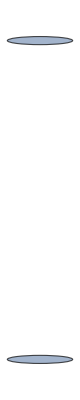
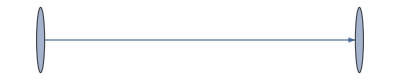
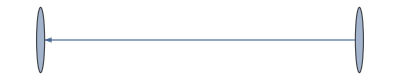

```mathematica
Map[AdjacencyGraph,ListDAG[2]]
```

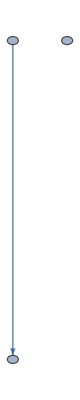
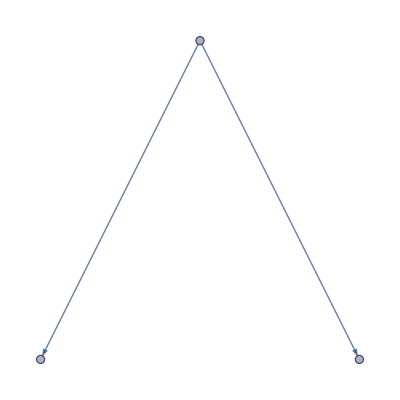
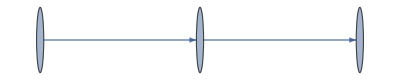
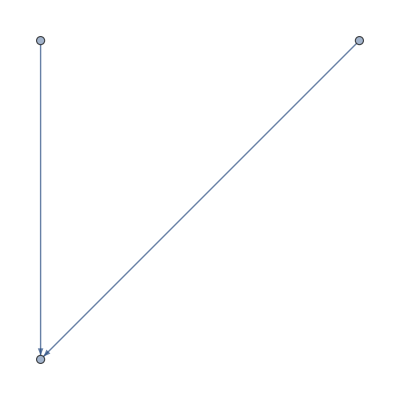
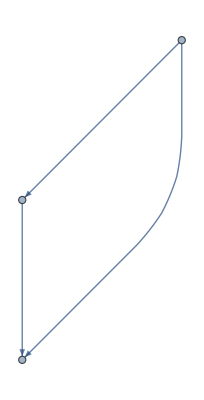
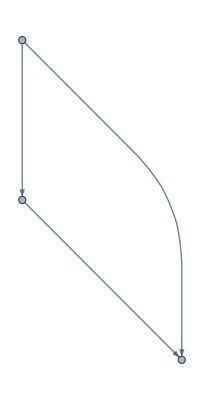
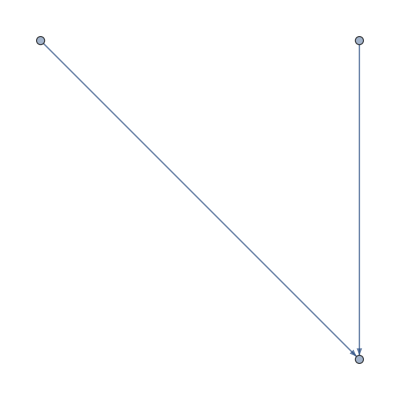
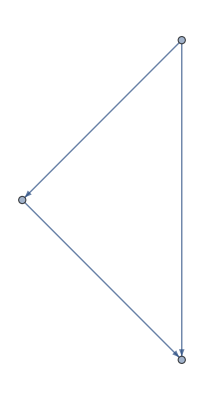
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Map[AdjacencyGraph,ListDAG[3]]
```

## MDL Score

A continuación se evalúan los DAG a partir de la métrica MDL que toma en cuenta la contribución a la longitud de la descripción de tres aspectos del modelo.

La contribución de las variables:

||X_i|| representa el número de valores diferentes que puede tomar la variable X. La contribución del DAG:

|Π_i| la cantidad de padres de X_i. La contribución de los parámetros:

||Π_i|| representa el número de configuraciones posibles de los padres de X_i. En total la contribución del modelo a la longitud de descripción es:

Por último es necesario calcular la contribución de los datos dado el modelo. El modelo está implícito en esta cálculo debido a que la probabilidad p(u_i) se calcula haciendo uso del DAG.

```mathematica
Parents[graph_,vertex_]:=Cases[graph, p_->vertex:>p];
PossibleValues[dataset_,attribute_]:=DeleteDuplicates[dataset[[All,attribute]]];
ParentConfigurations[dataset_,parents_]:=Tuples[Map[PossibleValues[dataset,#]&,parents]];
NodeParentConfigurations[dag_,dataset_,node_]:=ParentConfigurations[dataset,Parents[dag,node]];

VariablesDL[dataset_]:=Block[{n = Length[First[dataset]]},
Sum[Log[Length[PossibleValues[dataset,i]]],{i,1,n}]+Log[n]
];

DAGDL[dag_]:=Block[{n = Length[VertexList[dag]]},
If[dag == {},Return[0]];
Log[n]*Sum[1+Length[Parents[dag,i]],{i,1,n}]
];
ParameterDL[dag_,dataset_]:=Block[{n = Length[First[dataset]],m=Length[dataset]},
1/2 Log[m]*Sum[Length[NodeParentConfigurations[dag,dataset,i]]*(Length[PossibleValues[dataset,i]]-1),{i,1,n}]
];
ModelDL[dag_,dataset_]:=VariablesDL[dataset] + DAGDL[dag] + ParameterDL[dag,dataset];
```

### Ejemplos

```mathematica
testData = Drop[Import[FileNameJoin[{NotebookDirectory[],"data3.dat"}]],1];
```

```mathematica
ModelDL[{1->2,1->3,1->4,2->3,2->4,3->4},testData]
```

3 Log[2]+Log[3]+10 Log[4]+(7 Log[500])/2

```mathematica
Parents[{1->2,1->3,1->4,2->3,2->4,3->4},3]
```

{1,2}

```mathematica
NodeParentConfigurations[{1->2,1->3,1->4,2->3,2->4,3->4},testData,3]
```

{{0,1},{0,0},{1,1},{1,0}}

```mathematica
AttributeValues[dag_,data_,attribute_]:=Block[{parents},
parents = Parents[dag,attribute];
Map[<|"ParentValues"->#[[parents]],"Value"->#[[attribute]]|>&,data]
];
AttributeProbability[dag_,data_,node_,nodeValue_,parentValues_]:=Block[{num,den},
num = Length[Cases[AttributeValues[dag,data,node],KeyValuePattern[{"ParentValues"->parentValues, "Value"->nodeValue}]]];
den = Length[Cases[AttributeValues[dag,data,node],KeyValuePattern["ParentValues"->parentValues]]];
If[den ≠ 0,
Return[num/den];
,
Return[0]
];
];

InstanceProbability[dag_,dataset_,instance_]:=Block[{n= Length[First[dataset]]},
Apply[Times,Table[AttributeProbability[dag,dataset,i,instance[[i]],instance[[Parents[dag,i]]]],{i,1,n}]]
];

DataDL[dag_,dataset_]:=-Total[Map[Log[InstanceProbability[dag,dataset,#]]&,dataset]];
MDLScore[dag_,dataset_]:=ModelDL[dag,dataset] + DataDL[dag,dataset];
```

## Bayesian Network Score

Debido a la alta cantidad de operaciones necesarias para obtener los parámetros de las redes bayesianas a partir del DAG y posteriormente hacer la búsqueda del mejor DAG bajo la métrica MDL, no fue posible reportar los resultados con n = 6 y ni siquiera fue posible realizar la prueba con 10000 ejemplos. En estos resultados se reporta hasta n = 4 con 500 ejemplos, e incluso con esta pequeña selección, la ejecución del programa fue tardada.

Los ejemplos a partir de un modelo de oro fueron generados con el software Tetrad.

```mathematica
Needs["AdvancedMapping`"];
```

#### n = 3

```mathematica
data = Drop[Import[FileNameJoin[{NotebookDirectory[],"data3.dat"}]],1];
dags = Map[EdgeList[AdjacencyGraph[#]]&,ListDAG[3]];
scores = ProgressMap[{#,N[MDLScore[#,data]]}&,dags];
```

```mathematica
scores
```

{{{},941.943},{{3->2},723.564},{{3->1},694.021},{{3->1,3->2},476.976},{{2->3},722.871},{{2->3,3->1},476.976},{{2->1},684.147},{{2->1,3->2},467.102},{{2->1,3->1},664.103},{{2->1,3->1,3->2},444.743},{{2->1,2->3},467.102},{{2->1,2->3,3->1},444.743},{{1->3},693.328},{{1->3,3->2},476.976},{{1->3,2->3},703.52},{{1->3,2->1},437.559},{{1->3,2->1,2->3},444.743},{{1->2},684.147},{{1->2,3->2},693.645},{{1->2,3->1},437.559},{{1->2,3->1,3->2},444.743},{{1->2,2->3},467.102},{{1->2,1->3},437.559},{{1->2,1->3,3->2},444.743},{{1->2,1->3,2->3},444.743}}

```mathematica
SortBy[scores,Last]
```

{{{1->2,1->3},437.559},{{1->2,3->1},437.559},{{1->3,2->1},437.559},{{1->2,1->3,2->3},444.743},{{1->2,1->3,3->2},444.743},{{1->2,3->1,3->2},444.743},{{1->3,2->1,2->3},444.743},{{2->1,2->3,3->1},444.743},{{2->1,3->1,3->2},444.743},{{1->2,2->3},467.102},{{2->1,2->3},467.102},{{2->1,3->2},467.102},{{1->3,3->2},476.976},{{2->3,3->1},476.976},{{3->1,3->2},476.976},{{2->1,3->1},664.103},{{1->2},684.147},{{2->1},684.147},{{1->3},693.328},{{1->2,3->2},693.645},{{3->1},694.021},{{1->3,2->3},703.52},{{2->3},722.871},{{3->2},723.564},{{},941.943}}

```mathematica
bestNets = Take[SortBy[scores,Last],4]
```

{{{1->2,1->3},437.559},{{1->2,3->1},437.559},{{1->3,2->1},437.559},{{1->2,1->3,2->3},444.743}}

Los mejores DAG seleccionados son:

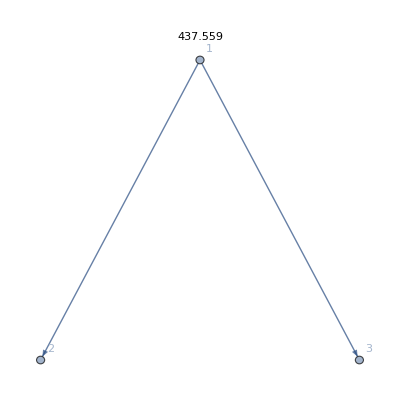
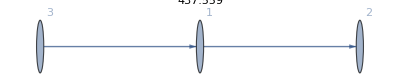
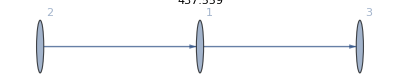
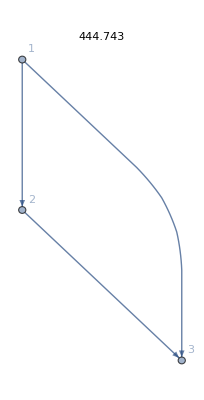

```mathematica
Map[Graph[First[#],VertexLabels->"Name",PlotLabel->Last[#]]&,bestNets]
```

### n = 4

```mathematica
data = Drop[Import[FileNameJoin[{NotebookDirectory[],"data4.dat"}]],1];
dags = Map[EdgeList[AdjacencyGraph[#]]&,ListDAG[4]];
scores = ProgressMap[{#,N[MDLScore[#,data]]}&,dags];
```

```mathematica
bestNets = Take[SortBy[scores,Last],10]
```

{{{1->3},497.299},{{3->1},497.992},{{1->3,3->2},499.438},{{2->3,3->1},499.438},{{3->1,3->2},499.438},{{1->3,2->3},501.32},{{1->3,3->4},502.96},{{3->1,3->4},502.96},{{1->3,1->4},503.04},{{1->4,3->1},503.04}}

Los mejores DAG seleccionados son:

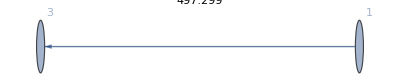
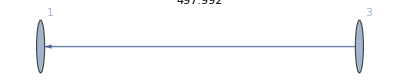
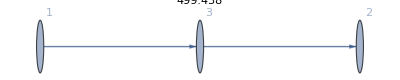
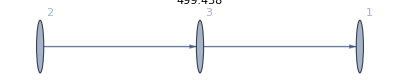
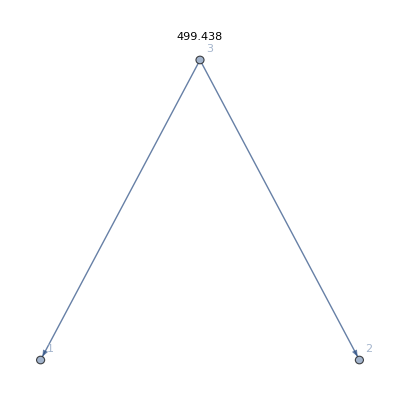
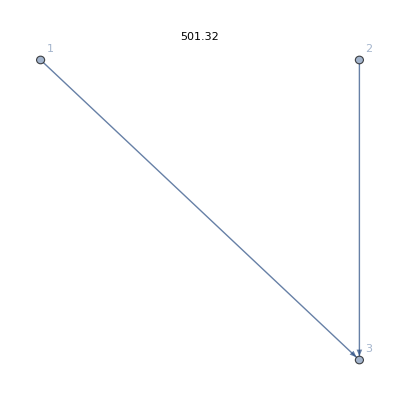
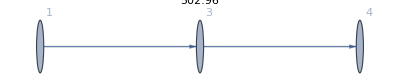
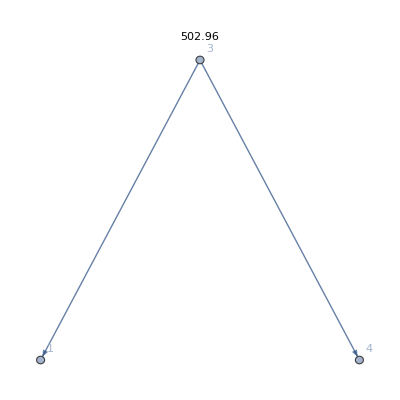

```mathematica
Map[Graph[First[#],VertexLabels->"Name",PlotLabel->Last[#]]&,bestNets]
```